```mathematica
ClearAll["Global`*"];
#sqrt2flip##
$Assumptions={ξ∈Reals,y∈Reals};
PE=1/2*(PauliMatrix[3]-IdentityMatrix[2]);
h1[n_,y_]:=Sqrt[n]/2*PauliMatrix[1]+y*PE;
h2[n_,ξ_,y_]:=Sqrt[n]/2*(Cos[ξ]*PauliMatrix[1]-Sin[ξ]*PauliMatrix[2])+y*PE;

U11=MatrixExp[-I*h1[1,0]*s1];
U12 =MatrixExp[-I*h2[1,ξ,y]*s2];
U21=MatrixExp[-I*h1[2,0]*s1];
U22 =MatrixExp[-I*h2[2,ξ,y]*s2];
s1=Pi/Sqrt[2];
s2 = 4Pi/Sqrt[2+y^2];
c1=TrigToExp[{0,1}.U12.U11.{1,0}];
c2=Simplify[{1,0}.U22.U21.{1,0}];
```

```mathematica
c1/.Exp[-I*ξ]-> (I* (-(ⅇ^((2 ⅈ π (y-√(1+y^2)))/(√(2+y^2))) (y-√(1+y^2)))/(2 √(1+y^2))+(ⅇ^((2 ⅈ π (y+√(1+y^2)))/(√(2+y^2))) (y+√(1+y^2)))/(2 √(1+y^2))) Sin[π/(2 √2)])/((ⅇ^((2 ⅈ π (y-√(1+y^2)))/(√(2+y^2)))-ⅇ^((2 ⅈ π (y+√(1+y^2)))/(√(2+y^2))))/(2 √(1+y^2))Cos[π/(2 √2)])//FullSimplify
```

0

```mathematica
c2
```

0

```mathematica
(*check if there is a solution for Exp[-I*ξ]=A/B*)

A=I* (-(ⅇ^((2 ⅈ π (y-√(1+y^2)))/(√(2+y^2))) (y-√(1+y^2)))/(2 √(1+y^2))+(ⅇ^((2 ⅈ π (y+√(1+y^2)))/(√(2+y^2))) (y+√(1+y^2)))/(2 √(1+y^2))) Sin[π/(2 √2)];
Aconj=-I* (-(ⅇ^((-2 ⅈ π (y-√(1+y^2)))/(√(2+y^2))) (y-√(1+y^2)))/(2 √(1+y^2))+(ⅇ^((-2 ⅈ π (y+√(1+y^2)))/(√(2+y^2))) (y+√(1+y^2)))/(2 √(1+y^2))) Sin[π/(2 √2)];
B=((ⅇ^((2 ⅈ π (y-√(1+y^2)))/(√(2+y^2)))-ⅇ^((2 ⅈ π (y+√(1+y^2)))/(√(2+y^2))))/(2 √(1+y^2))Cos[π/(2 √2)]);
Bconj=(ⅇ^((-2 ⅈ π (y-√(1+y^2)))/(√(2+y^2)))-ⅇ^((-2 ⅈ π (y+√(1+y^2)))/(√(2+y^2))))/(2 √(1+y^2))Cos[π/(2 √2)];
f1=A*Aconj;
f2 = B*Bconj;
```

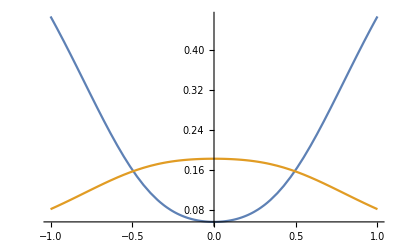

```mathematica
Plot[{f1,f2},{y,-1,1}]
```

```mathematica
FindRoot[f1==f2,{y,0.5}]
```

{y→0.49408-1.82216×10^-17 ⅈ}

```mathematica
y=0.4940804772277263;
```

```mathematica
(*Compute value for Exp[-I*ξ]*)
 (I* (-(ⅇ^((2 ⅈ π (y-√(1+y^2)))/(√(2+y^2))) (y-√(1+y^2)))/(2 √(1+y^2))+(ⅇ^((2 ⅈ π (y+√(1+y^2)))/(√(2+y^2))) (y+√(1+y^2)))/(2 √(1+y^2))) Sin[π/(2 √2)])/((ⅇ^((2 ⅈ π (y-√(1+y^2)))/(√(2+y^2)))-ⅇ^((2 ⅈ π (y+√(1+y^2)))/(√(2+y^2))))/(2 √(1+y^2))Cos[π/(2 √2)])
```

```mathematica
-0.07677029594602053-0.9970488060573373 ⅈ; (*negative cos and positive sin)*)
```

```mathematica
ξ=ArcCos[-0.07677029594602053]
```

1.64764

```mathematica
c1
c2
```

5.55112×10^-17-5.55112×10^-17 ⅈ

```mathematica
0
```

```mathematica
s2
```

8.38856

```mathematica
N[s1]
```

2.22144